```mathematica
(* Set directory is required for each cold start. *)
SetDirectory[NotebookDirectory[]];
```

```mathematica
niceticks[min_,max_]:={#,NumberForm[#,DigitBlock->3],{0.02,0}}&/@FindDivisions[{min,max},6]
```

```mathematica
plot[values_]:=ListLinePlot[values, PlotLegends->{"Astro", "TURF"}, Frame->True,FrameTicks->{{niceticks,None},{Automatic,None}}]
```

```mathematica
browsers = {"chrome", "chrome-simd", "safari", "firefox"};
browser = "firefox"
```

firefox

Area

```mathematica
areaFiles = FileNames["./bench/" <> browser <> "/area-*.json"];
areaJSON = Import[#1]&/@areaFiles;
areaJSONValues = Transpose@Values@areaJSON;
```

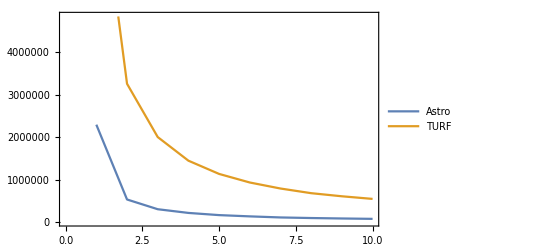

```mathematica
(* Show plot of ops/sec - higher is better - in relation to n polygon size. *)
areaPlot = plot[areaJSONValues]
```

```mathematica
astroMean = AccountingForm@Mean[areaJSONValues[[1]]]
turfMean = AccountingForm@Mean[areaJSONValues[[2]]]
```

397131.

2019711.

```mathematica
Export[browser <>"_area.png",areaPlot]
```

firefox_area.png

Union

```mathematica
unionFiles = FileNames["./bench/" <> browser <> "/union-*.json"];
unionJSON = Import[#1]&/@unionFiles;
unionJSONValues = Transpose@Values@unionJSON;
```

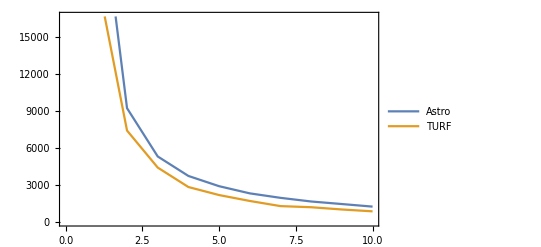

```mathematica
(* Show plot of ops/sec - higher is better - in relation to n polygon size. *)
unionPlot = plot[unionJSONValues]
```

```mathematica
unionAstroMean = AccountingForm@Mean[unionJSONValues[[1]]]
unionTurfMean = AccountingForm@Mean[unionJSONValues[[2]]]
```

5901.77

4302.2

```mathematica
Export[browser <>"_union.png" , unionPlot]
```

firefox_union.png

# Difference

```mathematica
differenceFiles = FileNames["./bench/"<>browser<>"/difference-*.json"];
differenceJSON = Import[#1]&/@differenceFiles;
differenceJSONValues = Transpose@Values@differenceJSON;
```

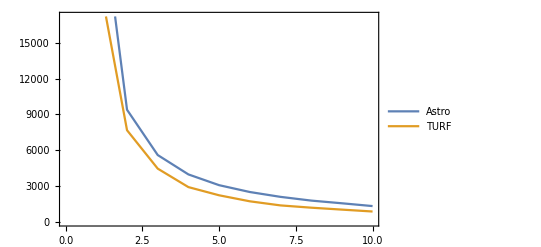

```mathematica
(* Show plot of ops/sec - higher is better - in relation to n polygon size. *)
differencePlot =plot[differenceJSONValues]
```

```mathematica
differenceAstroMean = Mean[differenceJSONValues[[1]]]
differenceTurfMean = Mean[differenceJSONValues[[2]]]
```

6072.81

4500.4

```mathematica
Export[browser<>"_difference.png", differencePlot]
```

firefox_difference.png

# Intersect

```mathematica
intersectFiles = FileNames["./bench/"<>browser<>"/intersect-*.json"];
intersectJSON = Import[#1]&/@intersectFiles;
intersectJSONValues = Transpose@Values@intersectJSON;
```

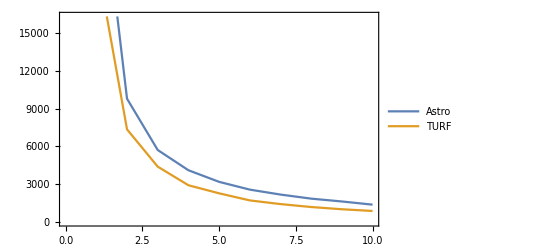

```mathematica
(* Show plot of ops/sec - higher is better - in relation to n polygon size. *)
intersectPlot = plot[intersectJSONValues]
```

```mathematica
intersectAstroMean = Mean[intersectJSONValues[[1]]]
intersectTurfMean = Mean[intersectJSONValues[[2]]]
```

6283.98

4412.17

```mathematica
Export[browser<>"_intersect.png", intersectPlot]
```

firefox_intersect.png